## Explicit analytical continuation for Gamma distributed interarrivals

```mathematica
Clear[k]
```

```mathematica
LaplaceTransform[(μ t)^(k-1)μ/Gamma[k] E^(-μ t),t,s]
```

μ^k (s+μ)^-k

n=λ b, a=γ/μ where μ=rate of the Gamma dist.

```mathematica
testsum[a_,n_,k_]:=Exp[-NSum[1/(m a^(k m))(Zeta[k m,1+1/a]-Zeta[k m,n+1+1/a]),{m,1,100},Method->"WynnEpsilon"]]
check[a_,n_,k_]:=Product[1-(1/(m a+1))^k,{m,1,n}]
```

```mathematica
testsum[1.2,3,2]
```

0.690505

```mathematica
check[1.2,3,2]//N
```

0.690505

```mathematica
a=2;
k=.3;
tabletest=Table[{x,E^x testsum[a,x,k]},{x,1,20,0.25}];
```

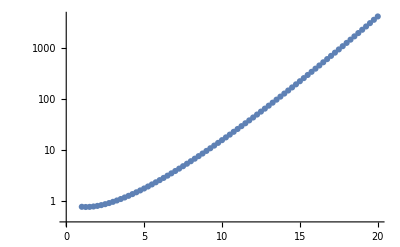

```mathematica
ListLogPlot[tabletest]
```

## Mean squared displacement <X_t^2> from the moments formula

```mathematica
Clear[μ,k,γ,m]
w[s_]:=μ^k (s+μ)^-k;
ψ[s_]:=w[s]/(1-w[s]);
```

We choose λ=1.

```mathematica
xmomentlaplace[s_,n_]:=ψ[s](n!)/(s+n γ)Product[1+ψ[s+m γ],{m,1,n-1}];
xmomentlaplace[s,2]//FullSimplify
```

(2 μ^k (s+γ+μ)^k)/((s+2 γ) (μ^k-(s+μ)^k) (μ^k-(s+γ+μ)^k))

```mathematica
xmoment2[t_]:=InverseLaplaceTransform[xmomentlaplace[s,2],s,t]
μ=1;
γ=0.5;
k=1.5;
xmoment2[1.3]
```

1.065

As expected, we quickly approach a stationary value.

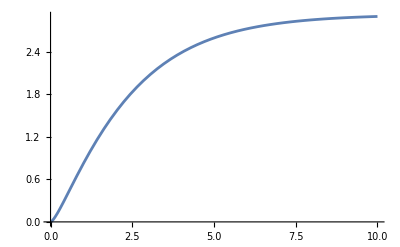

```mathematica
Plot[xmoment2[t],{t,0,10}]
```